# The Hadron Resonance Gas

```mathematica
SetDirectory[NotebookDirectory[]]
Needs["ErrorBarPlots`"]
```

/Users/fabian/Desktop/GIT/Strangeness/resonancegas

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

Notes:
• Have really all resonances up to 2.6 (or 3) GeV and J/Psi been included?
• Following the arguments of [nucl-th/1506.01260], f_0(500) has been excluded from the HRG for now.

## Lattice data

#### new

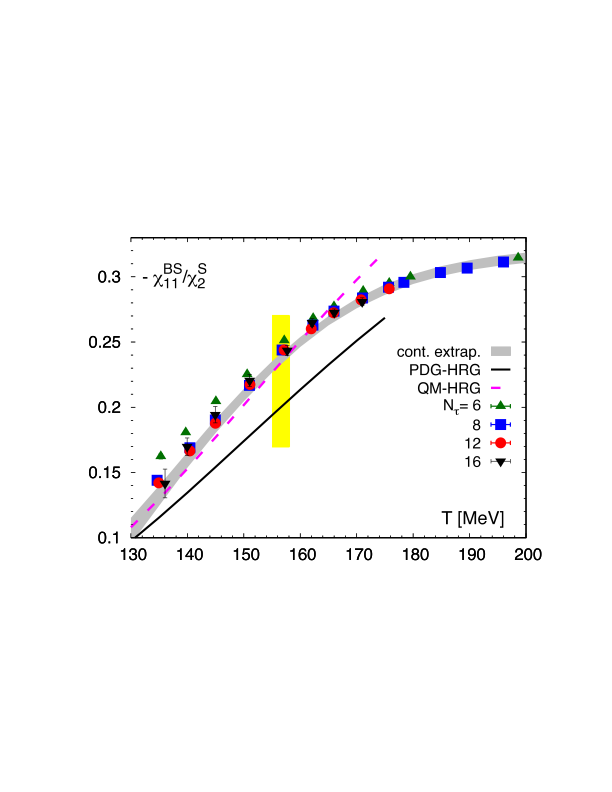

```mathematica
CBSthird1=Import["chiBS_S2_HRG_large.pdf"]
```

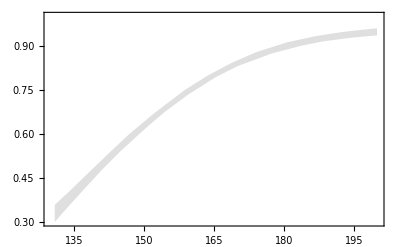

```mathematica
(* extract data with https://apps.automeris.io/wpd/ *)
CBS1low={{130.90322580645162,3 0.10001219842775819},{134.29032258064515,3 0.12022770398481972},{137.96774193548387,3 0.14170777988614797},
{141.06451612903226,3 0.1593982108972621},{144.93548387096774,3 0.18004066142586067},{149,3 0.19984548658172946},{151.32258064516128,3 0.21080238547031716},{154.51612903225805,3 0.22513282732447817},{159.4516129032258,3 0.24452968284087828},{165.3548387096774,3 0.2643602602331255},{170.09677419354838,3 0.2770317159121713},{177.4516129032258,3 0.2914204391433993},{183.5483870967742,3 0.2999091894822445},{188.29032258064515,3 0.3050176199512063},{194.5806451612903,3 0.30930740037950666},{199.90322580645162,3 0.31190295473027924}};
CBS1up={{130.1290322580645,3  0.11554757386825695},{134.48387096774192,3  0.13703713743561938},{138.16129032258064,3  0.15599620493358632},{142.80645161290323,3  0.17959067497966924},{146.7741935483871,3  0.19939414475467604},{152.29032258064515,3 0.223841149362971},{158.67741935483872,3  0.24956085660070476},{163.70967741935482,3 0.2664380590946056},{168.83870967741936,3  0.28079560856600705},{174.16129032258064, 3 0.2930550284629981},{180.74193548387098, 3 0.30407156410951475},{186.64516129032256,3 0.3108769314177284},{192.35483870967744, 3 0.31557874762808347},{196.61290322580646, 3 0.31815939278937383},{199.90322580645162, 3 0.31988614800759013}};
ListPlot[{CBS1up,CBS1low},Frame->True,Joined->True,PlotRange->{{130,200},{0.3,1.00}},PlotStyle->Opacity[0],Filling->{1->{{2},Opacity[.25,Gray]}}]
```

#### old

{T,muB,p,dp,e,de,s,ds,nB,dnB,nQ,dnQ,nS,dnS}

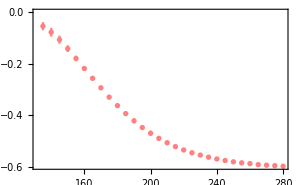
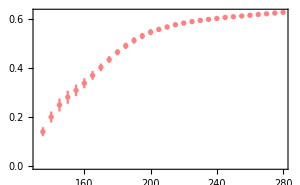
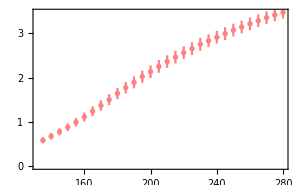

```mathematica
(*data for finite Subscript[μ, B]/T, Subscript[μ, S]=Subscript[μ, Q]=0*)
HotQCDmuTdatRAW=Import["./lqcd_eos_muQ=muS=0.txt"];
HotQCDmuTdat=ToExpression["{"<>StringReplace[ToString[Drop[StringSplit[ToString[FullForm[HotQCDmuTdatRAW]]],78]],{"\\n#,"->"","|, "->"","\\n"->"},{","\\n#,"->"","\""->"","e+"->" 10^","e-"->" 10^-"}]<>"}"];
(*picks out separate Subscript[μ, B]/T*)
HotQCDmuTdatSEQ[n_]:=HotQCDmuTdat[[#]]&/@Range[2+(n-1) 30,31+(n-1) 30,1](*n∈[1,23]*);

(*in terms of Subscript[μ, B]*)
HotQCDmu=Table[HotQCDmuTdat[[n,1]] HotQCDmuTdat[[n,2]],{n,Length[HotQCDmuTdat]}];
Clear[HotQCDmudat];
HotQCDmudat=HotQCDmuTdat;
HotQCDmudat[[All,2]]=HotQCDmu;
HotQCDmudatSEQ[n_]:=HotQCDmudat[[#]]&/@Range[2+(n-1) 30,31+(n-1) 30,1](*n∈[1,23]*);

HotQCDmuTdat[[1]]

ExtractMuTab[X__,mu_]:=Module[{MuTab,MuPos,MuRes},
MuTab=Table[Round[X[[n,2]],.1],{n,1,Length[X]}];
MuPos=Flatten[Position[MuTab,mu]];
MuRes=Drop[Table[X[[MuPos[[n]]]],{n,1,Length[MuPos]}],None,{2}]
];

(*find Subscript[μ, B] that have been computed by the lattice*)
MuOverlapPos[n_]:=Flatten[Select[Position[Round[HotQCDmudatSEQ[n][[All,2]],.1],#]&/@Range[0.,675.,15.],UnsameQ[#,{}]&]];

(*n=16 has the largest overlap with my result (corresponds to Subscript[μ, B]/T=1.5)*)
HotQCDmudatSEQol[n_]:=HotQCDmudatSEQ[n][[#]]&/@MuOverlapPos[n];

(*strangeness number*)
nsHotQCDmu[n_]:=HotQCDmuTdatSEQ[n][[All,{1,13}]];
dnsHotQCDmu[n_]:=HotQCDmuTdatSEQ[n][[All,{1,14}]];
nsHotQCDmuerr[n_]:=Table[{{nsHotQCDmu[n][[m,1]],nsHotQCDmu[n][[m,2]]},ErrorBar[dnsHotQCDmu[n][[m,2]]]},{m,Length[nsHotQCDmu[n]]}];

(*baryon number*)
nBHotQCDmu[n_]:=HotQCDmuTdatSEQ[n][[All,{1,9}]];
dnBHotQCDmu[n_]:=HotQCDmuTdatSEQ[n][[All,{1,10}]];
nBHotQCDmuerr[n_]:=Table[{{nBHotQCDmu[n][[m,1]],nBHotQCDmu[n][[m,2]]},ErrorBar[dnBHotQCDmu[n][[m,2]]]},{m,Length[nBHotQCDmu[n]]}];

(*pressure*)
pHotQCDmu[n_]:=HotQCDmuTdatSEQ[n][[All,{1,3}]];
dpHotQCDmu[n_]:=HotQCDmuTdatSEQ[n][[All,{1,4}]];
pHotQCDmuerr[n_]:=Table[{{pHotQCDmu[n][[m,1]],pHotQCDmu[n][[m,2]]},ErrorBar[dpHotQCDmu[n][[m,2]]]},{m,Length[pHotQCDmu[n]]}];



CompN=21;

{Show[
ErrorListPlot[nsHotQCDmuerr[CompN],Frame->True,PlotStyle->Pink,ImageSize->300]
],
Show[
ErrorListPlot[nBHotQCDmuerr[CompN],Frame->True,PlotStyle->Pink,ImageSize->300]
],
Show[
ErrorListPlot[pHotQCDmuerr[CompN],PlotStyle->Pink,Frame->True,ImageSize->300]
]
}
```

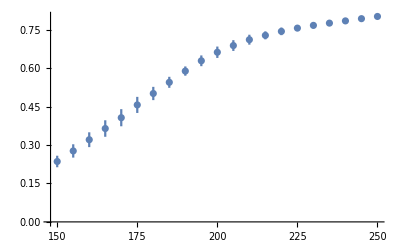
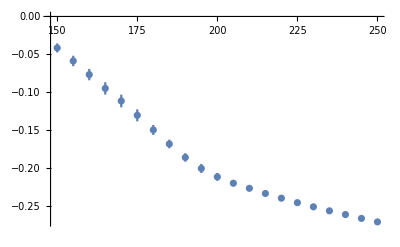
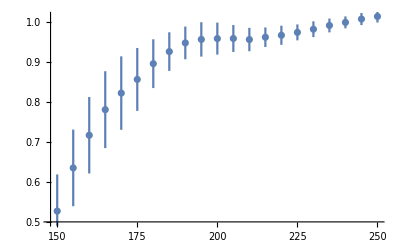

```mathematica
(*second order cumulants*)
(*continuum extrapolated*)
Import["./table_chi2_extrap_rev2.txt"];
HotQCDchi2raw="{{150 &   0.0790( 57)  &   0.3736(126)  &   0.2358(225)  &  -0.0415( 60)  &   0.0187( 29)  &   0.0929( 61) \\
155 &   0.1026( 77)  &   0.3998(158)  &   0.2770(260)  &  -0.0587( 69)  &   0.0221( 24)  &   0.1031( 68) \\
160 &   0.1247( 98)  &   0.4258(198)  &   0.3208(289)  &  -0.0767( 75)  &   0.0242( 23)  &   0.1173( 70) \\
165 &   0.1470(109)  &   0.4513(232)  &   0.3645(322)  &  -0.0949( 81)  &   0.0259( 21)  &   0.1332( 78) \\
170 &   0.1662(111)  &   0.4734(240)  &   0.4067(334)  &  -0.1115( 84)  &   0.0269( 21)  &   0.1491( 84) \\
175 &   0.1849( 99)  &   0.4964(222)  &   0.4567(314)  &  -0.1304( 79)  &   0.0270( 19)  &   0.1655( 83) \\
180 &   0.2024( 74)  &   0.5118(179)  &   0.5013(259)  &  -0.1497( 66)  &   0.0263( 17)  &   0.1782( 77) \\
185 &   0.2182( 56)  &   0.5239(144)  &   0.5449(215)  &  -0.1682( 57)  &   0.0249( 19)  &   0.1892( 76) \\
190 &   0.2326( 52)  &   0.5379(115)  &   0.5888(181)  &  -0.1860( 56)  &   0.0233( 22)  &   0.2005( 72) \\
195 &   0.2445( 55)  &   0.5522( 84)  &   0.6289(210)  &  -0.2005( 60)  &   0.0220( 21)  &   0.2122( 68) \\
200 &   0.2524( 46)  &   0.5638( 68)  &   0.6623(222)  &  -0.2116( 52)  &   0.0205( 21)  &   0.2235( 70) \\
205 &   0.2570( 41)  &   0.5717( 57)  &   0.6884(210)  &  -0.2200( 38)  &   0.0186( 18)  &   0.2335( 67) \\
210 &   0.2604( 38)  &   0.5770( 55)  &   0.7113(194)  &  -0.2267( 31)  &   0.0168( 15)  &   0.2424( 62) \\
215 &   0.2637( 36)  &   0.5792( 63)  &   0.7282(155)  &  -0.2335( 32)  &   0.0152( 14)  &   0.2486( 51) \\
220 &   0.2676( 35)  &   0.5809( 84)  &   0.7438(148)  &  -0.2397( 35)  &   0.0140( 12)  &   0.2537( 57) \\
225 &   0.2713( 28)  &   0.5824( 63)  &   0.7565(113)  &  -0.2456( 34)  &   0.0128( 12)  &   0.2576( 56) \\
230 &   0.2749( 27)  &   0.5841( 64)  &   0.7672(116)  &  -0.2511( 33)  &   0.0119( 12)  &   0.2606( 56) \\
235 &   0.2784( 23)  &   0.5855( 56)  &   0.7760(105)  &  -0.2564( 28)  &   0.0109( 10)  &   0.2628( 48) \\
240 &   0.2819( 20)  &   0.5873( 46)  &   0.7847( 92)  &  -0.2613( 24)  &   0.0101(  8)  &   0.2649( 39) \\
245 &   0.2852( 20)  &   0.5890( 45)  &   0.7934( 98)  &  -0.2664( 23)  &   0.0093(  8)  &   0.2667( 37) \\
250 &   0.2885( 20)  &   0.5907( 45)  &   0.8020( 98)  &  -0.2710( 23)  &   0.0085(  7)  &   0.2688( 34)}}";

Clear[HotQCDchi2,HotQCDchi2err];

HotQCDchi2=ToExpression[StringReplace[HotQCDchi2raw,{" \\"->"},{","&"->",","("~~Shortest[___]~~")"->""}]];
HotQCDchi2err=ToExpression[StringReplace[HotQCDchi2raw,{" \\"->"},{","&"~~Shortest[___]~~"("->",",")"->""}]];

SmallestDecimalFac[X_]:=Module[{testdat,base,signumb},
testdat=X;
base=Last[RealDigits[testdat]];
(*signumb=Length[ToExpression[StringReplace[ToString[RealDigits[testdat][[1]]],", 0"->""]]];*)
signumb=Length[Internal`DeleteTrailingZeros@RealDigits[testdat,10,4][[1]]];
10^(base-signumb)//N
];
Do[
HotQCDchi2err[[All,n]];
HotQCDchi2err[[All,n]]=SmallestDecimalFac[HotQCDchi2[[3,n]]] HotQCDchi2err[[All,n]];
,{n,2,7,1}];

(*chiS2*)
chiS2HotQCD=HotQCDchi2[[All,{1,4}]];
dchiS2HotQCD=HotQCDchi2err[[All,{1,4}]];
chiS2HotQCDerr=Table[{{chiS2HotQCD[[n,1]],chiS2HotQCD[[n,2]]},ErrorBar[dchiS2HotQCD[[n,2]]]},{n,Length[chiS2HotQCD]}];
(*chiBS11*)
chiBS11HotQCD=HotQCDchi2[[All,{1,5}]];
dchiBS11HotQCD=HotQCDchi2err[[All,{1,5}]];
chiBS11HotQCDerr=Table[{{chiBS11HotQCD[[n,1]],chiBS11HotQCD[[n,2]]},ErrorBar[dchiBS11HotQCD[[n,2]]]},{n,Length[chiBS11HotQCD]}];
(*CBS*)
CBSHotQCD=Table[{chiS2HotQCD[[n,1]],-3 chiBS11HotQCD[[n,2]]/chiS2HotQCD[[n,2]]},{n,Length[chiS2HotQCD]}];
dCBSHotQCD=Table[{CBSHotQCD[[n,1]],CBSHotQCD[[n,2]] √((dchiBS11HotQCD[[n,2]]/chiBS11HotQCD[[n,2]])^2+(dchiS2HotQCD[[n,2]]/chiS2HotQCD[[n,2]])^2)},{n,Length[CBSHotQCD]}];
CBSHotQCDerr=Table[{{CBSHotQCD[[n,1]],CBSHotQCD[[n,2]]},ErrorBar[dCBSHotQCD[[n,2]]]},{n,Length[CBSHotQCD]}];


{ErrorListPlot[chiS2HotQCDerr],ErrorListPlot[chiBS11HotQCDerr],ErrorListPlot[CBSHotQCDerr]}
```

## Vanishing chemical potential (Eduardo’s version)

```mathematica
(*
 - all entries in the list with # in front will be excluded
- for now, f0(600) has been excluded (following [nucl-th/1506.01260])
*)
thres=Select[Import["eos_particles.data","Table"][[2;;]],Length[#]==13&&Characters[#[[1]]][[1]]≠"#"&];
(*masses*)
mass=thres[[;;,2]]*1000;
(*spin*)
spin=thres[[;;,4]];
(*spin statistics*)
sign=If[Mod[Round[#*2+1],2]==1,1,-1]&/@spin;
(*p/T^4*)
adimensionalPressureHRG[T_]=Sum[1/(2π^2) Sum[((mass[[i]]/T)^2 ((2*spin[[i]]+1)/n^2)BesselK[2,n*mass[[i]]/T])(sign[[i]])^(n+1),{i,1,Length[thres]}],{n,1,5}];
teos=Import["eos.dat","Table"];
```

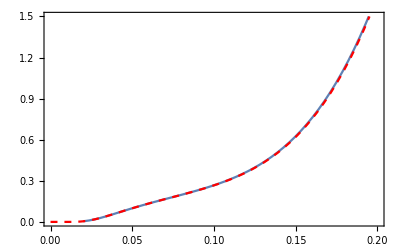

```mathematica
Show[{ListPlot[Transpose[{teos[[;;,1]],teos[[;;,3]]}],PlotRange->{{0.0,0.2},{0.,1.5}},Joined->True,Frame->True],Plot[adimensionalPressureHRG[T*1000],{T,0.0,0.2},PlotRange->{{0.0,0.2},{0.,1.5}},PlotStyle->{Dashed,Red},Frame->True]}]
```

## Finite chemical potential (Fabian’s version)

```mathematica
(*Subscript[I, 3]*)
iso3=thres[[;;,6]];
(*# light quarks*)
Nq=thres[[;;,7]];
(*# stange quarks*)
Ns=thres[[;;,8]];
(*# anti-light quarks*)
Nqb=thres[[;;,9]];
(*# anti-strange quarks*)
Nsb=thres[[;;,10]];
(*# charm quarks*)
Nc=thres[[;;,11]];
(*# anti-charm quarks*)
Ncb=thres[[;;,12]];

(*baryon number*)
BB = 1/3(Nq+Ns+Nc)- 1/3(Nqb+Nsb+Ncb);
(*strangeness*)
SS=Nsb-Ns;
(*charm*)
CC=Nc-Ncb;
(*charge (via Gell-Mann--Nishijima)*)
QQ=iso3+(BB+SS+CC)/2;

(*pressure at finite chemical potentials*)
PressureOfMu[T_,muB_,muS_,muQ_]=
Sum[
(2*spin[[i]]+1)/(2 π^2) Sum[
T^2 sign[[i]]^(k+1)/k^2 mass[[i]]^2 Exp[k (muB BB[[i]]+muS SS[[i]]+muQ QQ[[i]])/T] BesselK[2,(k mass[[i]])/T]
,{k,1,5}]
,{i,1,Length[thres]}];
```

### pressure

```mathematica
HotQCDmuTdatSEQ[21][[All,{1,2}]]
```

{{135.,2.},{140.,2.},{145.,2.},{150.,2.},{155.,2.},{160.,2.},{165.,2.},{170.,2.},{175.,2.},{180.,2.},{185.,2.},{190.,2.},{195.,2.},{200.,2.},{205.,2.},{210.,2.},{215.,2.},{220.,2.},{225.,2.},{230.,2.},{235.,2.},{240.,2.},{245.,2.},{250.,2.},{255.,2.},{260.,2.},{265.,2.},{270.,2.},{275.,2.},{280.,2.}}

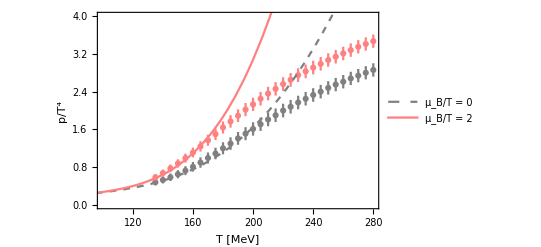

```mathematica
(*Subscript[μ, B]/T = 0 & 2*)
Show[
ErrorListPlot[{pHotQCDmuerr[1],pHotQCDmuerr[21]},PlotStyle->{Gray,Pink},Frame->True,PlotRange->{{100,280},{0,4}},FrameLabel->{"T [MeV]","p/T^4"},LabelStyle->13],
Plot[{PressureOfMu[T,0,0,0]/T^4,PressureOfMu[T,2 T,0,0]/T^4},{T,0,280},Frame->True,PlotStyle->{{Dashed,Gray},{Pink}},PlotLegends->{"μ_B/T = 0","μ_B/T = 2"}]
]
```

### off-diagonal cumulants

```mathematica
(*off-diagonal susceptibilities*)
chi[B_,S_,Q_][T_,muB_,muS_,muQ_]:=(Tx^(B+S+Q-4) D[PressureOfMu[Tx,muBx,muSx,muQx],{muBx,B},{muSx,S},{muQx,Q}])/.{Tx->T,muBx->muB,muSx->muS,muQx->muQ};
```

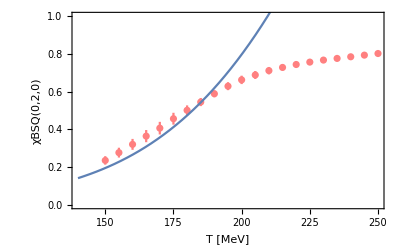

```mathematica
Show[
ErrorListPlot[chiS2HotQCDerr,PlotStyle->{Pink},Frame->True,PlotRange->{{140,250},{0,1.}},FrameLabel->{"T [MeV]","χBSQ(0,2,0)"},LabelStyle->13,ImageSize->400],
Plot[chi[0,2,0][T,0,0,0],{T,140,250}]
]
```

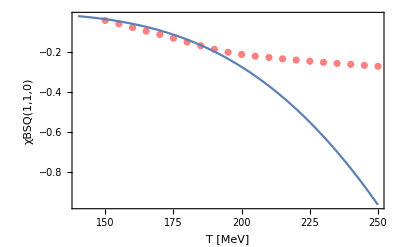

```mathematica
Show[
ErrorListPlot[chiBS11HotQCDerr,PlotStyle->{Pink},Frame->True,PlotRange->{{140,250},{0,-.3}},FrameLabel->{"T [MeV]","χBSQ(1,1,0)"},LabelStyle->13,ImageSize->400],
Plot[chi[1,1,0][T,0,0,0],{T,140,250}]
]
```

```mathematica
(*baryon-strangeness correlation*)
CBSHRG[T_,muB_,muS_,muQ_]=-3chi[1,1,0][T,muB,muS,muQ]/chi[0,2,0][T,muB,muS,muQ];
```

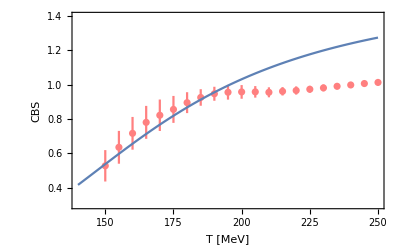

```mathematica
Show[
ErrorListPlot[CBSHotQCDerr,PlotStyle->{Pink},Frame->True,PlotRange->{{140,250},{0.3,1.4}},FrameLabel->{"T [MeV]","CBS"},LabelStyle->13,ImageSize->400],
Plot[CBSHRG[T,0,0,0],{T,140,250},Frame->True]
]
```

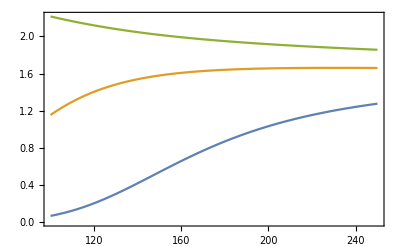

```mathematica
Plot[{CBSHRG[T,0,0,0],CBSHRG[T,420,0,0],CBSHRG[T,675,0,0]},{T,100,250},Frame->True]
```

### higher order baryon number correlations

```mathematica
(*perform the derivative explicitly at muB=0*)
(*DPressureOfMu[T_,n_]=
Sum[
(2*spin[[i]]+1)/(2 π^2) Sum[
T^2 sign[[i]]^(k+1)/k^2 mass[[i]]^2 (k BB[[i]]/T)^n BesselK[2,(k mass[[i]])/T]
,{k,1,5}]
,{i,1,Length[thres]}];
chiExplt[B_][T_]:=(Tx^(B-4) DPressureOfMu[Tx,B])/.{Tx->T};
LogPlot[{chiExplt[8][T],chi8ofT},{T,10,200},Frame->True]*)
```

```mathematica
chi2ofTmu0=chi[2,0,0][T,0,0,0];
chi4ofTmu0=chi[4,0,0][T,0,0,0];
chi6ofTmu0=chi[6,0,0][T,0,0,0];
chi8ofTmu0=chi[8,0,0][T,0,0,0];
```

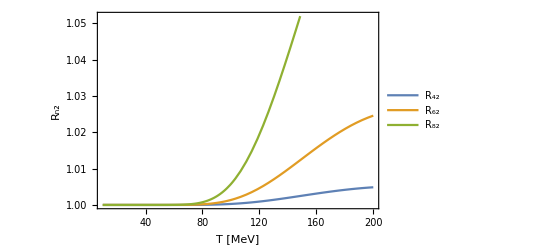

```mathematica
Plot[{chi4ofTmu0/chi2ofTmu0,chi6ofTmu0/chi2ofTmu0,chi8ofTmu0/chi2ofTmu0},{T,10,200},(*PlotRange->{0,2},*)Frame->True,PlotLegends->{"R_42","R_62","R_82"},FrameLabel->{"T [MeV]","R_n2"}]
```

```mathematica
R42ofTmu0Tab=Table[{T,chi4ofTmu0/chi2ofTmu0},{T,5,200,1}];
R62ofTmu0Tab=Table[{T,chi6ofTmu0/chi2ofTmu0},{T,5,200,1}];
R82ofTmu0Tab=Table[{T,chi8ofTmu0/chi2ofTmu0},{T,5,200,1}];
R42ofTmu0Tab>>R42ofTmu0.dat
R62ofTmu0Tab>>R62ofTmu0.dat
R82ofTmu0Tab>>R82ofTmu0.dat
```

### μ_S at strangeness neutrality (and vanishing μ_Q)

```mathematica
(*strangeness chemical potential at strangeness neutrality, Subscript[μ, S0](T,Subscript[μ, B])*)
muS0[T_,muB_]:=muS/.FindRoot[chi[0,1,0][T,muB,muS,0],{muS,0}];
```

```mathematica
muS0list={};
Do[
AppendTo[muS0list,{T,muB,muS0[T,muB]}],
{T,80,200,5},
{muB,0,600,20}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
ListPlot3D[muS0list,AxesLabel->{"T","μ_B"}]
```

-Graphics3D-

### C_BS at strangeness neutrality (and vanishing μ_Q)

#### Data from [Fu, Pawlowski, Rennecke (2018)]

```mathematica
CBSofTmu2s[15]={0.969390464030877-0.026358172429373043 T+0.00021949477606636675 T^2-4.599816153885925*^-7 T^3+0.08115883152919887 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},0,T]+0.34431598933651014 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T]+0.2516199705567234 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.1384733172683837 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]-1.9749962127674465 √(0.007848729362502126-0.00031078844228011584 T+4.980616461671664*^-6 T^2-4.1502798118311795*^-8 T^3+1.909246619984105*^-10 T^4-4.616465698632625*^-13 T^5+4.591825703262712*^-16 T^6+0.0001315948704026649 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},0,T]^2+0.0000846551274365542 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T]^2+0.0006397531016681216 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]-0.000010941062414006611 T BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+4.951139161061341*^-8 T^2 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]-6.163459213601337*^-11 T^3 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.00008491103624428924 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]^2+BSplineBasis[{3,{90,111,132,153,174,195,216,237}},0,T] (0.0014604938815633724-0.000027867262367057482 T+1.547537518245043*^-7 T^2-2.6614222238224763*^-10 T^3+0.00006791696943408295 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T]+0.0001389465506820923 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.000058737263486925844 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T])+BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T] (0.0005167095134267836-8.193284735766897*^-6 T+3.125486327871471*^-8 T^2-2.45493892771944*^-11 T^3+0.00003888147977805368 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.00012272359611253958 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T])-0.00017693102852364793 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+6.628780399536883*^-6 T BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]-6.683205178906314*^-8 T^2 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+1.7716694147449932*^-10 T^3 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+0.00005222408278026749 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T] BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+0.00011511737891386517 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]^2),0.969390464030877-0.026358172429373043 T+0.00021949477606636675 T^2-4.599816153885925*^-7 T^3+0.08115883152919887 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},0,T]+0.34431598933651014 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T]+0.2516199705567234 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.1384733172683837 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+1.9749962127674465 √(0.007848729362502126-0.00031078844228011584 T+4.980616461671664*^-6 T^2-4.1502798118311795*^-8 T^3+1.909246619984105*^-10 T^4-4.616465698632625*^-13 T^5+4.591825703262712*^-16 T^6+0.0001315948704026649 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},0,T]^2+0.0000846551274365542 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T]^2+0.0006397531016681216 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]-0.000010941062414006611 T BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+4.951139161061341*^-8 T^2 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]-6.163459213601337*^-11 T^3 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.00008491103624428924 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]^2+BSplineBasis[{3,{90,111,132,153,174,195,216,237}},0,T] (0.0014604938815633724-0.000027867262367057482 T+1.547537518245043*^-7 T^2-2.6614222238224763*^-10 T^3+0.00006791696943408295 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T]+0.0001389465506820923 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.000058737263486925844 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T])+BSplineBasis[{3,{90,111,132,153,174,195,216,237}},1,T] (0.0005167095134267836-8.193284735766897*^-6 T+3.125486327871471*^-8 T^2-2.45493892771944*^-11 T^3+0.00003888147977805368 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T]+0.00012272359611253958 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T])-0.00017693102852364793 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+6.628780399536883*^-6 T BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]-6.683205178906314*^-8 T^2 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+1.7716694147449932*^-10 T^3 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+0.00005222408278026749 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},2,T] BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]+0.00011511737891386517 BSplineBasis[{3,{90,111,132,153,174,195,216,237}},3,T]^2)};
CBSofTmu2s[630]={-0.1214362109058115+0.03542012481297301 T-0.0002498419599773995 T^2+5.012825557095787*^-7 T^3+0.5217611682422135 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},0,T]-0.3019661008587627 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T]-0.3095207620851942 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]-0.17048414239474433 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]-0.12071483345697896 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]-1.975092072712088 √(0.010318407490432814-0.0004060581223277211 T+6.4144498038655934*^-6 T^2-5.220303717684382*^-8 T^3+2.3248939259857628*^-10 T^4-5.40588927945979*^-13 T^5+5.150843662289629*^-16 T^6+0.00015946268048592084 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},0,T]^2+0.00009044877918653056 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T]^2+0.0013913494036225885 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]-0.000026150383040933023 T BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+1.4118059014474432*^-7 T^2 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]-2.3405099429836206*^-10 T^3 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+0.0001361712279525325 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]^2+0.0007348306736275622 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]-0.000013558128342603687 T BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+7.127591160472122*^-8 T^2 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]-1.140191160639822*^-10 T^3 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.00003174333176018939 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T] BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.0000758335888786487 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]^2+BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T] (0.0011384441140371193-0.00002168645943143116 T+1.2071679538504154*^-7 T^2-2.08322345879176*^-10 T^3+0.000052969801206958696 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+0.00009488989124691414 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.00005412212886542347 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T])+BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},0,T] (0.001998022403613895-0.00003908709765120681 T+2.2414727854368488*^-7 T^2-3.9949424859106553*^-10 T^3+0.00009082087048913428 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T]+0.00021389065187463386 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+0.00008728394428474672 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.00009626945115222132 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T])+0.00036902206400945214 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]-5.361142702645091*^-6 T BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+1.3922570709205311*^-8 T^2 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+9.304671156769361*^-12 T^3 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+0.00013981013590849998 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T] BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+0.00002226847286751968 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T] BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+0.00009754000407514696 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]^2),-0.1214362109058115+0.03542012481297301 T-0.0002498419599773995 T^2+5.012825557095787*^-7 T^3+0.5217611682422135 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},0,T]-0.3019661008587627 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T]-0.3095207620851942 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]-0.17048414239474433 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]-0.12071483345697896 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+1.975092072712088 √(0.010318407490432814-0.0004060581223277211 T+6.4144498038655934*^-6 T^2-5.220303717684382*^-8 T^3+2.3248939259857628*^-10 T^4-5.40588927945979*^-13 T^5+5.150843662289629*^-16 T^6+0.00015946268048592084 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},0,T]^2+0.00009044877918653056 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T]^2+0.0013913494036225885 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]-0.000026150383040933023 T BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+1.4118059014474432*^-7 T^2 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]-2.3405099429836206*^-10 T^3 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+0.0001361712279525325 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]^2+0.0007348306736275622 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]-0.000013558128342603687 T BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+7.127591160472122*^-8 T^2 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]-1.140191160639822*^-10 T^3 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.00003174333176018939 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T] BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.0000758335888786487 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]^2+BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T] (0.0011384441140371193-0.00002168645943143116 T+1.2071679538504154*^-7 T^2-2.08322345879176*^-10 T^3+0.000052969801206958696 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+0.00009488989124691414 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.00005412212886542347 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T])+BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},0,T] (0.001998022403613895-0.00003908709765120681 T+2.2414727854368488*^-7 T^2-3.9949424859106553*^-10 T^3+0.00009082087048913428 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},1,T]+0.00021389065187463386 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T]+0.00008728394428474672 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T]+0.00009626945115222132 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T])+0.00036902206400945214 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]-5.361142702645091*^-6 T BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+1.3922570709205311*^-8 T^2 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+9.304671156769361*^-12 T^3 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+0.00013981013590849998 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},2,T] BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+0.00002226847286751968 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},3,T] BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]+0.00009754000407514696 BSplineBasis[{3,{90,107,124,141,158,175,192,209,226}},4,T]^2)};
CBSofTmu2s[675]={0.14729686228599687+0.03485676221241405 T-0.00025968020283116883 T^2+5.328011705348048*^-7 T^3+1.1489321079487467 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},0,T]-0.7357726681778357 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T]-0.32119985527019945 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]-0.3178134102955682 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]-0.24613757202694778 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]-0.16202850881701966 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]-0.07942018964905835 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]-1.9752875077034413 √(0.24150241942704176-0.009544556493784058 T+0.00015115671450769794 T^2-1.2319088543169192*^-6 T^3+5.493518460908627*^-9 T^4-1.2795487812653102*^-11 T^5+1.2218701867808804*^-14 T^6+0.003401207354116029 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},0,T]^2+0.002200111703617161 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T]^2+0.03891995410197954 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]-0.0007408064889889134 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+4.056705167130715*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]-6.841908186466016*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+0.00344848461532498 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]^2+0.027638371909783355 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]-0.0005144628525438651 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+2.7196191767924657*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]-4.3822479527502014*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.0020913602024446283 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.0025786769713903824 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]^2+0.02201096637647867 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]-0.00039213090365233067 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+1.8953089693580268*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]-2.6622303167887252*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.004282507889795438 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.0014524569097289501 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.0027551593310295515 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]^2+0.012451953770903544 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]-0.0002171792239914043 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+1.004976663493086*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]-1.3013250998800441*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0017165828121919228 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0025023651140781995 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0006381361626409257 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0016726528196720025 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]^2+BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T] (0.029343151699315322-0.0005608642080393826 T+3.109996042750213*^-6 T^2-5.3339481280287876*^-9 T^3+0.001877442885042619 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+0.0031990911567327768 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.001988563690831847 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.00162000618671255 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0012368595929191373 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T])+BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},0,T] (0.04481904768580108-0.0008780455789215463 T+5.011763384942265*^-6 T^2-8.873019766879118*^-9 T^3+0.002365867118432381 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T]+0.005290409423157242 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+0.003165266287368341 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.0033584075964304375 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.001794595339990242 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.00146112100565097 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T])+0.0030335130830465907 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]-9.723758116913876*^-6 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]-4.0757498986072463*^-7 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+1.6617186777764629*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0022629516379054984 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0016708366836012934 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0031411740403705073 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0006610412819620096 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.00216729717974206 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]^2),0.14729686228599687+0.03485676221241405 T-0.00025968020283116883 T^2+5.328011705348048*^-7 T^3+1.1489321079487467 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},0,T]-0.7357726681778357 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T]-0.32119985527019945 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]-0.3178134102955682 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]-0.24613757202694778 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]-0.16202850881701966 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]-0.07942018964905835 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+1.9752875077034413 √(0.24150241942704176-0.009544556493784058 T+0.00015115671450769794 T^2-1.2319088543169192*^-6 T^3+5.493518460908627*^-9 T^4-1.2795487812653102*^-11 T^5+1.2218701867808804*^-14 T^6+0.003401207354116029 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},0,T]^2+0.002200111703617161 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T]^2+0.03891995410197954 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]-0.0007408064889889134 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+4.056705167130715*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]-6.841908186466016*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+0.00344848461532498 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]^2+0.027638371909783355 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]-0.0005144628525438651 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+2.7196191767924657*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]-4.3822479527502014*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.0020913602024446283 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.0025786769713903824 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]^2+0.02201096637647867 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]-0.00039213090365233067 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+1.8953089693580268*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]-2.6622303167887252*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.004282507889795438 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.0014524569097289501 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.0027551593310295515 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]^2+0.012451953770903544 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]-0.0002171792239914043 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+1.004976663493086*^-6 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]-1.3013250998800441*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0017165828121919228 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0025023651140781995 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0006381361626409257 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0016726528196720025 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]^2+BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T] (0.029343151699315322-0.0005608642080393826 T+3.109996042750213*^-6 T^2-5.3339481280287876*^-9 T^3+0.001877442885042619 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+0.0031990911567327768 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.001988563690831847 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.00162000618671255 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.0012368595929191373 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T])+BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},0,T] (0.04481904768580108-0.0008780455789215463 T+5.011763384942265*^-6 T^2-8.873019766879118*^-9 T^3+0.002365867118432381 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},1,T]+0.005290409423157242 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T]+0.003165266287368341 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T]+0.0033584075964304375 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T]+0.001794595339990242 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T]+0.00146112100565097 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T])+0.0030335130830465907 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]-9.723758116913876*^-6 T BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]-4.0757498986072463*^-7 T^2 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+1.6617186777764629*^-9 T^3 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0022629516379054984 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},2,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0016708366836012934 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},3,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0031411740403705073 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},4,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.0006610412819620096 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},5,T] BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]+0.00216729717974206 BSplineBasis[{3,{90,104,118,132,146,160,174,188,202,216,230}},6,T]^2)};
CBSofTmu2s[570]={-3.578249598410954+0.14129186934870458 T-0.0015447279799250177 T^2+7.91289069592168*^-6 T^3-1.9625557427992825*^-8 T^4+1.9196165299348016*^-11 T^5+0.47551400125821275 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]-0.26271925615908004 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]-0.030589454368500947 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-0.07027219924900242 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-1.9751891630765606 √(0.8393007716690312-0.05789367131449189 T+0.0017598147115065604 T^2-0.000031043253654918156 T^3+3.520774914905534*^-7 T^4-2.6849678966974167*^-9 T^5+1.3960430831426395*^-11 T^6-4.893666666427777*^-14 T^7+1.1083932625484908*^-16 T^8-1.4667384263420102*^-19 T^9+8.621812961411905*^-23 T^10+0.0002930579716047687 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]^2+0.00019667260984976688 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]^2-0.01844751958787589 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.0006212208877907192 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-7.872460751798441*^-6 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+4.685678401835787*^-8 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-1.3223684041568502*^-10 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+1.4290817001493174*^-13 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00019765963453657559 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]^2+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T] (-0.02676457080908795+0.0009199455050378315 T-0.00001196041404770813 T^2+7.348178825805448*^-8 T^3-2.1523540832518743*^-10 T^4+2.426091955443065*^-13 T^5+0.0003283669314247556 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]+0.0004256433615957127 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.0001465283971010463 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T] (-0.016770377328746092+0.0005564736559014647 T-6.928374023910528*^-6 T^2+4.037454962484177*^-8 T^3-1.1117199760826769*^-10 T^4+1.1679560414004588*^-13 T^5+0.0002793228239108598 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00026682357901301046 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])-0.0030397176088608493 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00007594028555636624 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-5.187864884267509*^-7 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-3.532401292528137*^-10 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+1.2840256133095957*^-11 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-2.8895802103522356*^-14 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.0001714172615138972 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T] BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00016276995963516964 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]^2),-3.578249598410954+0.14129186934870458 T-0.0015447279799250177 T^2+7.91289069592168*^-6 T^3-1.9625557427992825*^-8 T^4+1.9196165299348016*^-11 T^5+0.47551400125821275 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]-0.26271925615908004 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]-0.030589454368500947 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-0.07027219924900242 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+1.9751891630765606 √(0.8393007716690312-0.05789367131449189 T+0.0017598147115065604 T^2-0.000031043253654918156 T^3+3.520774914905534*^-7 T^4-2.6849678966974167*^-9 T^5+1.3960430831426395*^-11 T^6-4.893666666427777*^-14 T^7+1.1083932625484908*^-16 T^8-1.4667384263420102*^-19 T^9+8.621812961411905*^-23 T^10+0.0002930579716047687 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]^2+0.00019667260984976688 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]^2-0.01844751958787589 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.0006212208877907192 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-7.872460751798441*^-6 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+4.685678401835787*^-8 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-1.3223684041568502*^-10 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+1.4290817001493174*^-13 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00019765963453657559 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]^2+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T] (-0.02676457080908795+0.0009199455050378315 T-0.00001196041404770813 T^2+7.348178825805448*^-8 T^3-2.1523540832518743*^-10 T^4+2.426091955443065*^-13 T^5+0.0003283669314247556 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]+0.0004256433615957127 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.0001465283971010463 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T] (-0.016770377328746092+0.0005564736559014647 T-6.928374023910528*^-6 T^2+4.037454962484177*^-8 T^3-1.1117199760826769*^-10 T^4+1.1679560414004588*^-13 T^5+0.0002793228239108598 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00026682357901301046 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])-0.0030397176088608493 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00007594028555636624 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-5.187864884267509*^-7 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-3.532401292528137*^-10 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+1.2840256133095957*^-11 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-2.8895802103522356*^-14 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.0001714172615138972 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T] BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00016276995963516964 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]^2)};
CBSofTmu2s[420]={7.180665311264416-0.26186098746060166 T+0.0038106793809784332 T^2-0.000025141403854506544 T^3+7.735408587015035*^-8 T^4-9.041517068319601*^-11 T^5-0.07074887022365481 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]-0.044317052602869854 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]-0.15951085444751223 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-0.06218294516051146 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-1.9751891630765606 √(0.45167551178122745-0.031155879396926035 T+0.0009470564513829673 T^2-0.00001670614153500246 T^3+1.8947293571458322*^-7 T^4-1.4449340329395044*^-9 T^5+7.512902350764763*^-12 T^6-2.6335605430816*^-14 T^7+5.964894957988593*^-17 T^8-7.893354226873808*^-20 T^9+4.639888241832095*^-23 T^10+0.00015771117312680108 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]^2+0.00010584072445279856 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]^2-0.009927660181198793 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00033431431483624225 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-4.236619170473462*^-6 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+2.5216302208119545*^-8 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-7.116416973180163*^-11 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+7.690701951917993*^-14 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00010637189861062577 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]^2+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T] (-0.014403538785934564+0.0004950750324850847 T-6.43657949386976*^-6 T^2+3.9544732280008706*^-8 T^3-1.1583042276417297*^-10 T^4+1.3056181557225877*^-13 T^5+0.00017671293392042083 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]+0.00022906291722181124 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00007885526974970618 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T] (-0.00902509448152004+0.000299470144442069 T-3.7285523720399776*^-6 T^2+2.1727842962031977*^-8 T^3-5.982797896825585*^-11 T^4+6.285436169544677*^-14 T^5+0.00015031950845371836 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00014359295341327897 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])-0.0016358450426804166 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00004086778959499187 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-2.791885347601482*^-7 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-1.9009861726285687*^-10 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+6.910072593862906*^-12 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-1.5550475638766897*^-14 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00009224938417304075 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T] BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00008759577889416793 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]^2),7.180665311264416-0.26186098746060166 T+0.0038106793809784332 T^2-0.000025141403854506544 T^3+7.735408587015035*^-8 T^4-9.041517068319601*^-11 T^5-0.07074887022365481 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]-0.044317052602869854 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]-0.15951085444751223 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-0.06218294516051146 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+1.9751891630765606 √(0.45167551178122745-0.031155879396926035 T+0.0009470564513829673 T^2-0.00001670614153500246 T^3+1.8947293571458322*^-7 T^4-1.4449340329395044*^-9 T^5+7.512902350764763*^-12 T^6-2.6335605430816*^-14 T^7+5.964894957988593*^-17 T^8-7.893354226873808*^-20 T^9+4.639888241832095*^-23 T^10+0.00015771117312680108 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T]^2+0.00010584072445279856 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]^2-0.009927660181198793 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00033431431483624225 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-4.236619170473462*^-6 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+2.5216302208119545*^-8 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]-7.116416973180163*^-11 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+7.690701951917993*^-14 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00010637189861062577 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]^2+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},0,T] (-0.014403538785934564+0.0004950750324850847 T-6.43657949386976*^-6 T^2+3.9544732280008706*^-8 T^3-1.1583042276417297*^-10 T^4+1.3056181557225877*^-13 T^5+0.00017671293392042083 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T]+0.00022906291722181124 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00007885526974970618 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])+BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},1,T] (-0.00902509448152004+0.000299470144442069 T-3.7285523720399776*^-6 T^2+2.1727842962031977*^-8 T^3-5.982797896825585*^-11 T^4+6.285436169544677*^-14 T^5+0.00015031950845371836 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T]+0.00014359295341327897 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T])-0.0016358450426804166 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00004086778959499187 T BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-2.791885347601482*^-7 T^2 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-1.9009861726285687*^-10 T^3 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+6.910072593862906*^-12 T^4 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]-1.5550475638766897*^-14 T^5 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00009224938417304075 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},2,T] BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]+0.00008759577889416793 BSplineBasis[{5,{80,98,116,134,152,170,188,206,224,242}},3,T]^2)};
CBSofTmu2s[300]={2.3965904873053376-0.10613239019850815 T+0.0016729266469208547 T^2-0.000011068930988815497 T^3+3.35969553769917*^-8 T^4-3.8704877899309654*^-11 T^5+0.07284540089940285 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.029552686567949984 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.0059511030712154685 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.975092072712088 √(0.42794067222523735-0.02914861712962257 T+0.0008750820356113254 T^2-0.00001524946323283221 T^3+1.7091633923042267*^-7 T^4-1.2886681181919316*^-9 T^5+6.628365717249203*^-12 T^6-2.300122602753809*^-14 T^7+5.16153235513925*^-17 T^8-6.773579609626401*^-20 T^9+3.952793080580587*^-23 T^10+0.00019207008683978221 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.000064723696258609 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.007559088231203074+0.0002514066912848471 T-3.1519217130572422*^-6 T^2+1.8605197444108043*^-8 T^3-5.215665435371168*^-11 T^4+5.603397811076779*^-14 T^5+0.00010661161440382247 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.01449803283072328+0.0004896061777174059 T-6.239880976571011*^-6 T^2+3.74915487163831*^-8 T^3-1.0718125932986285*^-10 T^4+1.1771068623881157*^-13 T^5+0.0001542292144023254 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.0002466033508173885 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.0066299717091008415 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.00021274093633592413 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-2.5235309744818126*^-6 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.370453277359321*^-8 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-3.4166684074251605*^-11 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+3.119374906662074*^-14 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.00012836238601301442 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2),2.3965904873053376-0.10613239019850815 T+0.0016729266469208547 T^2-0.000011068930988815497 T^3+3.35969553769917*^-8 T^4-3.8704877899309654*^-11 T^5+0.07284540089940285 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.029552686567949984 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.0059511030712154685 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.975092072712088 √(0.42794067222523735-0.02914861712962257 T+0.0008750820356113254 T^2-0.00001524946323283221 T^3+1.7091633923042267*^-7 T^4-1.2886681181919316*^-9 T^5+6.628365717249203*^-12 T^6-2.300122602753809*^-14 T^7+5.16153235513925*^-17 T^8-6.773579609626401*^-20 T^9+3.952793080580587*^-23 T^10+0.00019207008683978221 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.000064723696258609 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.007559088231203074+0.0002514066912848471 T-3.1519217130572422*^-6 T^2+1.8605197444108043*^-8 T^3-5.215665435371168*^-11 T^4+5.603397811076779*^-14 T^5+0.00010661161440382247 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.01449803283072328+0.0004896061777174059 T-6.239880976571011*^-6 T^2+3.74915487163831*^-8 T^3-1.0718125932986285*^-10 T^4+1.1771068623881157*^-13 T^5+0.0001542292144023254 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.0002466033508173885 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.0066299717091008415 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.00021274093633592413 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-2.5235309744818126*^-6 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.370453277359321*^-8 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-3.4166684074251605*^-11 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+3.119374906662074*^-14 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.00012836238601301442 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2)};
CBSofTmu2s[180]={4.313634734478155-0.14608746250034146 T+0.0017930694472838712 T^2-9.659902865249896*^-6 T^3+2.424483704333469*^-8 T^4-2.3249090735193852*^-11 T^5+0.10689103313670165 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.11124142980535841 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.054881337540771215 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.975092072712088 √(0.21800886954081725-0.014849387967878129 T+0.00044579928415565883 T^2-7.768642842959824*^-6 T^3+8.707112999548593*^-8 T^4-6.564953926894988*^-10 T^5+3.376735633485288*^-12 T^6-1.1717678663824555*^-14 T^7+2.6294762495722855*^-17 T^8-3.450712982621461*^-20 T^9+2.0136995778998492*^-23 T^10+0.00009784763454899789 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.0000329726543178768 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.0038508802434570086+0.00012807590425328692 T-1.6057059638002823*^-6 T^2+9.478178461707086*^-9 T^3-2.6570536508152115*^-11 T^4+2.854578921017773*^-14 T^5+0.00005431191528312077 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.0073858362925785905+0.0002494235679196966 T-3.178827080627443*^-6 T^2+1.909958712382266*^-8 T^3-5.4602113561587654*^-11 T^4+5.99661946277696*^-14 T^5+0.0000785700889499056 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.00012562890425236355 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.003377553785371265 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.000108378132871743 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.2855803869664816*^-6 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+6.981597897718914*^-9 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.7405777609905246*^-11 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.5891254120324898*^-14 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.00006539256603198127 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2),4.313634734478155-0.14608746250034146 T+0.0017930694472838712 T^2-9.659902865249896*^-6 T^3+2.424483704333469*^-8 T^4-2.3249090735193852*^-11 T^5+0.10689103313670165 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.11124142980535841 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.054881337540771215 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.975092072712088 √(0.21800886954081725-0.014849387967878129 T+0.00044579928415565883 T^2-7.768642842959824*^-6 T^3+8.707112999548593*^-8 T^4-6.564953926894988*^-10 T^5+3.376735633485288*^-12 T^6-1.1717678663824555*^-14 T^7+2.6294762495722855*^-17 T^8-3.450712982621461*^-20 T^9+2.0136995778998492*^-23 T^10+0.00009784763454899789 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.0000329726543178768 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.0038508802434570086+0.00012807590425328692 T-1.6057059638002823*^-6 T^2+9.478178461707086*^-9 T^3-2.6570536508152115*^-11 T^4+2.854578921017773*^-14 T^5+0.00005431191528312077 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.0073858362925785905+0.0002494235679196966 T-3.178827080627443*^-6 T^2+1.909958712382266*^-8 T^3-5.4602113561587654*^-11 T^4+5.99661946277696*^-14 T^5+0.0000785700889499056 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.00012562890425236355 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.003377553785371265 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.000108378132871743 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.2855803869664816*^-6 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+6.981597897718914*^-9 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.7405777609905246*^-11 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.5891254120324898*^-14 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.00006539256603198127 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2)};
CBSofTmu1s[0]={12.92913522113079-0.4083585420625235 T+0.004777329516665729 T^2-0.00002568710342651719 T^3+6.51695907719125*^-8 T^4-6.31499852552162*^-11 T^5-0.12812548993292416 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.15724039359764555 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]-0.08799708137850507 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-0.9975973642180032 √(17.277341630303976-1.176823445130158 T+0.03532987693172826 T^2-0.0006156698884973707 T^3+6.900442455562393*^-6 T^4-5.2027677599114405*^-8 T^5+2.6760844757292407*^-10 T^6-9.2863349007512*^-13 T^7+2.083876659161567*^-15 T^8-2.7347119956380407*^-18 T^9+1.5958697286699478*^-21 T^10+0.007754487298525504 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.002613103835214444 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.3051847096117256+0.010150096906859292 T-0.00012725321934298577 T^2+7.511516740617857*^-7 T^3-2.10573192512178*^-9 T^4+2.262271958611968*^-12 T^5+0.004304253844896514 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.5853322257995857+0.019766976466024433 T-0.00025192406882959106 T^2+1.5136544326434199*^-6 T^3-4.32725224311838*^-9 T^4+4.752359080781785*^-12 T^5+0.006226729543481865 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.009956170599758325 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.2676732866304784 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.008589035991166406 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-0.00010188306368278149 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+5.532960757897866*^-7 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.3794189508933014*^-9 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.2593920006517168*^-12 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.0051824024673694305 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2),12.92913522113079-0.4083585420625235 T+0.004777329516665729 T^2-0.00002568710342651719 T^3+6.51695907719125*^-8 T^4-6.31499852552162*^-11 T^5-0.12812548993292416 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.15724039359764555 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]-0.08799708137850507 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.9975973642180032 √(17.277341630303976-1.176823445130158 T+0.03532987693172826 T^2-0.0006156698884973707 T^3+6.900442455562393*^-6 T^4-5.2027677599114405*^-8 T^5+2.6760844757292407*^-10 T^6-9.2863349007512*^-13 T^7+2.083876659161567*^-15 T^8-2.7347119956380407*^-18 T^9+1.5958697286699478*^-21 T^10+0.007754487298525504 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.002613103835214444 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.3051847096117256+0.010150096906859292 T-0.00012725321934298577 T^2+7.511516740617857*^-7 T^3-2.10573192512178*^-9 T^4+2.262271958611968*^-12 T^5+0.004304253844896514 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.5853322257995857+0.019766976466024433 T-0.00025192406882959106 T^2+1.5136544326434199*^-6 T^3-4.32725224311838*^-9 T^4+4.752359080781785*^-12 T^5+0.006226729543481865 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.009956170599758325 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.2676732866304784 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.008589035991166406 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-0.00010188306368278149 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+5.532960757897866*^-7 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.3794189508933014*^-9 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.2593920006517168*^-12 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.0051824024673694305 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2)};
CBSofTmu2s[0]={12.92913522113079-0.4083585420625235 T+0.004777329516665729 T^2-0.00002568710342651719 T^3+6.51695907719125*^-8 T^4-6.31499852552162*^-11 T^5-0.12812548993292416 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.15724039359764555 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]-0.08799708137850507 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.975092072712088 √(17.277341630303976-1.176823445130158 T+0.03532987693172826 T^2-0.0006156698884973707 T^3+6.900442455562393*^-6 T^4-5.2027677599114405*^-8 T^5+2.6760844757292407*^-10 T^6-9.2863349007512*^-13 T^7+2.083876659161567*^-15 T^8-2.7347119956380407*^-18 T^9+1.5958697286699478*^-21 T^10+0.007754487298525504 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.002613103835214444 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.3051847096117256+0.010150096906859292 T-0.00012725321934298577 T^2+7.511516740617857*^-7 T^3-2.10573192512178*^-9 T^4+2.262271958611968*^-12 T^5+0.004304253844896514 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.5853322257995857+0.019766976466024433 T-0.00025192406882959106 T^2+1.5136544326434199*^-6 T^3-4.32725224311838*^-9 T^4+4.752359080781785*^-12 T^5+0.006226729543481865 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.009956170599758325 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.2676732866304784 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.008589035991166406 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-0.00010188306368278149 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+5.532960757897866*^-7 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.3794189508933014*^-9 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.2593920006517168*^-12 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.0051824024673694305 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2),12.92913522113079-0.4083585420625235 T+0.004777329516665729 T^2-0.00002568710342651719 T^3+6.51695907719125*^-8 T^4-6.31499852552162*^-11 T^5-0.12812548993292416 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]+0.15724039359764555 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]-0.08799708137850507 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.975092072712088 √(17.277341630303976-1.176823445130158 T+0.03532987693172826 T^2-0.0006156698884973707 T^3+6.900442455562393*^-6 T^4-5.2027677599114405*^-8 T^5+2.6760844757292407*^-10 T^6-9.2863349007512*^-13 T^7+2.083876659161567*^-15 T^8-2.7347119956380407*^-18 T^9+1.5958697286699478*^-21 T^10+0.007754487298525504 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T]^2+0.002613103835214444 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]^2+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T] (-0.3051847096117256+0.010150096906859292 T-0.00012725321934298577 T^2+7.511516740617857*^-7 T^3-2.10573192512178*^-9 T^4+2.262271958611968*^-12 T^5+0.004304253844896514 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])+BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},0,T] (-0.5853322257995857+0.019766976466024433 T-0.00025192406882959106 T^2+1.5136544326434199*^-6 T^3-4.32725224311838*^-9 T^4+4.752359080781785*^-12 T^5+0.006226729543481865 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},1,T]+0.009956170599758325 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T])-0.2676732866304784 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.008589035991166406 T BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-0.00010188306368278149 T^2 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+5.532960757897866*^-7 T^3 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]-1.3794189508933014*^-9 T^4 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+1.2593920006517168*^-12 T^5 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]+0.0051824024673694305 BSplineBasis[{5,{80,100,120,140,160,180,200,220,240}},2,T]^2)};
```

#### Crossover transitions [Fu, Pawlowski, Rennecke (2018)]

```mathematica
chiPBns0muq={{5.,176.4458941518588},{10.,176.4105625162874},{15.,176.29112988642046},{20.,176.19230764923051},{25.,175.98739675723363},{30.,175.64807269149006},{35.,175.4375723112225},{40.,175.07434678983174},{45.,174.79557938757586},{50.,174.27955775406662},{55.,173.90104803928696},{60.,173.32950673235786},{65.,172.82860910895187},{70.,172.29455566565434},{75.,171.66151325576908},{80.,170.93796520477184},{85.,170.18574887975427},{90.,169.43499570028914},{95.,168.48851539616098},{100.,167.71292311905395},{105.,166.62214924281307},{110.,165.57847818758768},{115.,164.37340296112453},{120.,163.221377965174},{125.,161.9887509879995},{130.,160.70844097324849},{135.,159.46087258044514},{140.,158.14475787458744},{145.,156.73760417361484},{150.,155.19708089240598},{155.,153.5441798074513},{160.,151.7610406450363},{165.,149.82358614280534},{170.,147.81701242950524},{175.,145.86119943235116},{180.,143.86521557916936},{185.,141.78076388165567},{190.,139.45938665483314},{195.,136.7839918362849},{200.,134.01629268815793},{205.,131.20598727636997},{210.,128.4726195105337},{215.,125.51080503422942},{220.,121.94134250366466},{225.,118.12858880863287}};
chiPBns0=Table[{3 chiPBns0muq[[n,1]],chiPBns0muq[[n,2]]},{n,Length[chiPBns0muq]}];

decPBns0muq={{0.,155.248011549924},{5.,155.0726884238329},{10.,154.81407671185664},{15.,154.5365480453986},{20.,154.46284038269278},{25.,154.38773301511256},{30.,154.84036843814079},{35.,155.1546232021914},{40.,153.60812092616268},{45.,154.1889709882047},{50.,153.26620336536814},{55.,154.17904341519434},{60.,153.0690161512399},{65.,152.45233157332126},{70.,151.80637001941182},{75.,151.28596439359984},{80.,150.9468542371341},{85.,150.67566290640752},{90.,150.0733785926136},{95.,148.9613231632064},{100.,148.87362129181713},{105.,147.8236641096941},{110.,147.34345817018308},{115.,146.48685177358968},{120.,145.73699600590214},{125.,144.73793086213993},{130.,143.84445331203187},{135.,142.80961257095922},{140.,141.9510134569225},{145.,140.66142714235218},{150.,139.4593028388223},{155.,138.01100455730293},{160.,136.8502589412564},{165.,135.58179941248258},{170.,133.78463929378003},{175.,131.86147899139897},{180.,130.33834668534206},{185.,128.84749563008648},{190.,126.66254870480044},{195.,124.02802116008436},{200.,121.41827556236647},{205.,119.44761948593857},{210.,116.61455880462226},{215.,113.95587019305667},{220.,110.8831087646471},{225.,107.59256510398743}};
decPBns0=Table[{3 decPBns0muq[[n,1]],decPBns0muq[[n,2]]},{n,Length[decPBns0muq]}];
```

#### HRG

```mathematica
CBSHRGnS0[T_,muB_]:=CBSHRG[T,muB,muS0[T,muB],0];

FPRmuBlist={0,15,180,300,420,570,630,675};
Do[
CBSHRGnS0ofTmu[muB]=Table[{T,CBSHRGnS0[T,muB]},{T,90,160,2}],
{muB,FPRmuBlist}
];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

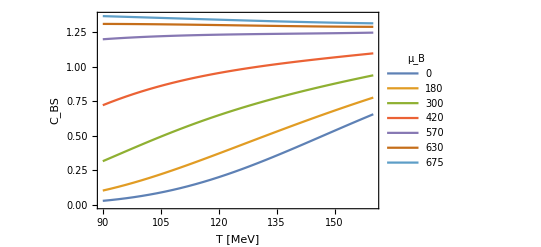

```mathematica
ListPlot[Table[CBSHRGnS0ofTmu[muB],{muB,FPRmuBlist}],Joined->True,Frame->True,FrameLabel->{"T [MeV]","C_BS"},LabelStyle->13,ImageSize->400,
PlotLegends->LineLegend[{"0","180","300","420","570","630","675"},LegendLabel->"μ_B"]]
```

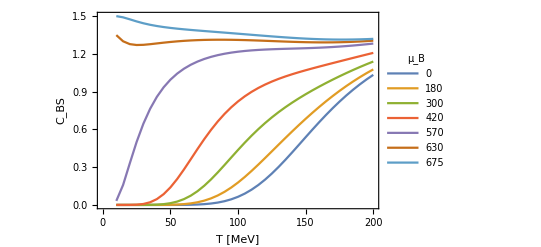
```mathematica
-Graphics-(*large T range*);
```

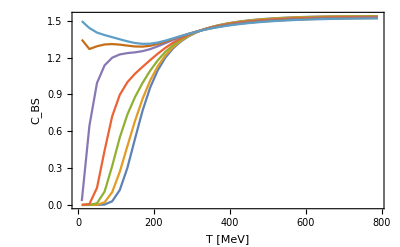
```mathematica
-Graphics-(*high temperature asymptotics*);
```

#### Plots

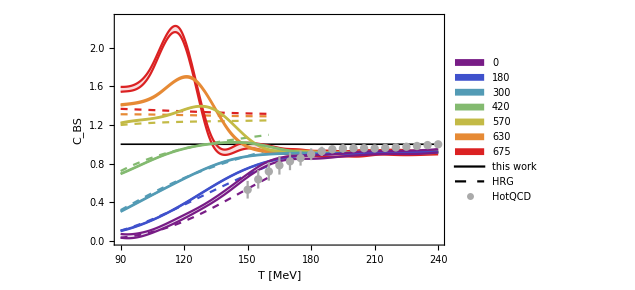

```mathematica
CBSofTPlot[mu_,Col_]:=Plot[CBSofTmu2s[mu],{T,90,240},PlotRange->{0,2.3},PlotStyle->Col,Filling->{1->{{2},Opacity[.15,Col]}},Frame->True]
ColDat[x_]:=ColorData["Rainbow",x]
Show[
Plot[1,{T,90,240},ImageSize->470,PlotStyle->{Black,Thickness[0.0025]}(*{Black,Dashing[.02]}*),Frame->True,PlotRange->{{90,240},{0,2.3}},AxesOrigin->{90,0},
FrameStyle->{{{Thickness[0.0025],Black},{Thickness[0.0025],Black}},{{Thickness[0.0025],Black},{Thickness[0.0025],Black}}},
FrameLabel->{Style["T [MeV]",FontFamily->"Helvetica"],Style["C_BS",FontFamily->"Helvetica"]},
LabelStyle->{FontFamily->"Helvetica",FontSize->15,Black},
PlotRegion->{{0.02,0.98},{0.02,0.98}},PlotLegends->Placed[SwatchLegend[Table[Directive[ColDat[(*1-*)n/6],Thick],{n,0,6}],{"0","180","300","420","570","630","675"},LegendLabel->"μ_B [MeV]",LabelStyle->{FontSize->14},LegendMarkerSize->7,LegendLayout->{"Row",2}],{0.72,0.8}]],
ListPlot[CBSHRGnS0ofTmu[675],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",6/6]}],
ListPlot[CBSHRGnS0ofTmu[630],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",5/6]}],
ListPlot[CBSHRGnS0ofTmu[570],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",4/6]}],
ListPlot[CBSHRGnS0ofTmu[420],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",3/6]}],
ListPlot[CBSHRGnS0ofTmu[300],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",2/6]}],
ListPlot[CBSHRGnS0ofTmu[180],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",1/6]}],
ListPlot[CBSHRGnS0ofTmu[0],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",0/6]},
PlotLegends->Placed[LineLegend[{Black,{Directive[Black,Dashed]}},{"this work","HRG"},LabelStyle->{FontSize->14},Spacings->.4],{.80,.22}]],
CBSofTPlot[675,ColorData["Rainbow",6/6]],
CBSofTPlot[630,ColorData["Rainbow",5/6]],
CBSofTPlot[570,ColorData["Rainbow",4/6]],
CBSofTPlot[420,ColorData["Rainbow",3/6]],
CBSofTPlot[300,ColorData["Rainbow",2/6]],
CBSofTPlot[180,ColorData["Rainbow",1/6]],
CBSofTPlot[0,ColorData["Rainbow",0/6]],
ErrorListPlot[CBSHotQCDerr,PlotStyle->{Lighter[Gray],AbsolutePointSize[6]},PlotLegends->Placed[PointLegend[{"    HotQCD"},LabelStyle->{FontSize->14},LegendMarkerSize->7],{.817,.10}]]
]
```

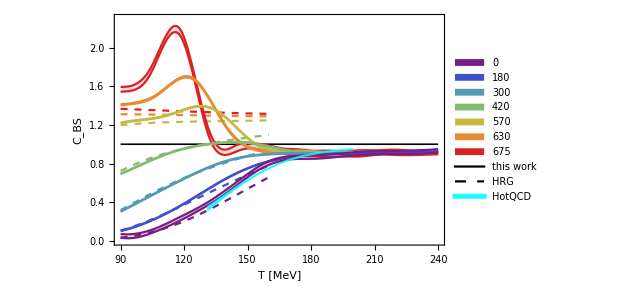

```mathematica
CBSofTPlot[mu_,Col_]:=Plot[CBSofTmu2s[mu],{T,90,240},PlotRange->{0,2.3},PlotStyle->Col,Filling->{1->{{2},Opacity[.15,Col]}},Frame->True]
ColDat[x_]:=ColorData["Rainbow",x]
CBSfinalPlot=Show[
Plot[1,{T,90,240},ImageSize->470,PlotStyle->{Black,Thickness[0.0025]}(*{Black,Dashing[.02]}*),Frame->True,PlotRange->{{90,240},{0,2.3}},AxesOrigin->{90,0},
FrameStyle->{{{Thickness[0.0025],Black},{Thickness[0.0025],Black}},{{Thickness[0.0025],Black},{Thickness[0.0025],Black}}},
FrameLabel->{Style["T [MeV]",FontFamily->"Helvetica"],Style["C_BS",FontFamily->"Helvetica"]},
LabelStyle->{FontFamily->"Helvetica",FontSize->15,Black},
PlotRegion->{{0.02,0.98},{0.02,0.98}},PlotLegends->Placed[SwatchLegend[Table[Directive[ColDat[(*1-*)n/6],Thick],{n,0,6}],{"0","180","300","420","570","630","675"},LegendLabel->"μ_B [MeV]",LabelStyle->{FontSize->14},LegendMarkerSize->7,LegendLayout->{"Row",2}],{0.72,0.8}]],
ListPlot[CBSHRGnS0ofTmu[675],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",6/6]}],
ListPlot[CBSHRGnS0ofTmu[630],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",5/6]}],
ListPlot[CBSHRGnS0ofTmu[570],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",4/6]}],
ListPlot[CBSHRGnS0ofTmu[420],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",3/6]}],
ListPlot[CBSHRGnS0ofTmu[300],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",2/6]}],
ListPlot[CBSHRGnS0ofTmu[180],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",1/6]}],
ListPlot[CBSHRGnS0ofTmu[0],Joined->True,PlotStyle->{Dashed,ColorData["Rainbow",0/6]},
PlotLegends->Placed[LineLegend[{Black,{Directive[Black,Dashed]},{Directive[Opacity[.9,Cyan],Thickness[.02]]}},{"this work","HRG","HotQCD"},LabelStyle->{FontSize->14},Spacings->.4],{.80,.18}]],
CBSofTPlot[675,ColorData["Rainbow",6/6]],
CBSofTPlot[630,ColorData["Rainbow",5/6]],
CBSofTPlot[570,ColorData["Rainbow",4/6]],
CBSofTPlot[420,ColorData["Rainbow",3/6]],
CBSofTPlot[300,ColorData["Rainbow",2/6]],
CBSofTPlot[180,ColorData["Rainbow",1/6]],
CBSofTPlot[0,ColorData["Rainbow",0/6]],
ListPlot[{CBS1up,CBS1low},Joined->True,PlotStyle->Opacity[0],Filling->{1->{{2},Opacity[.9,Cyan]}}]
]
```

### Freeze-out

```mathematica
Tcflim=158.4;aa=1307.5;
Tchemfreeze[sqrts_]:=Tcflim/(1+Exp[2.60-Log[sqrts]/0.45]);
muBchemfreeze[sqrts_]:=aa/(1+0.288 sqrts);
sqrtsCF[muB_]:=(aa/muB-1)/0.288
```

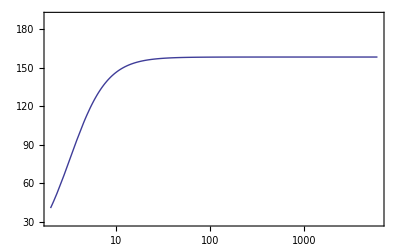
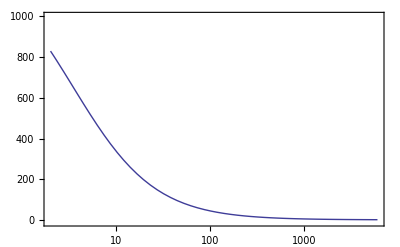

```mathematica
{LogLinearPlot[Tchemfreeze[sq],{sq,2,6 10^3},PlotRange->{30,190},Frame->True],
LogLinearPlot[muBchemfreeze[sq],{sq,2,6 10^3},PlotRange->{-10,1000},Frame->True]}
```

Power::infy: Infinite expression 1/0 encountered.

{{0,158.4},{15,158.393},{180,156.158},{300,149.806},{420,136.48},{570,107.192},{630,92.0637},{675,80.0591}}

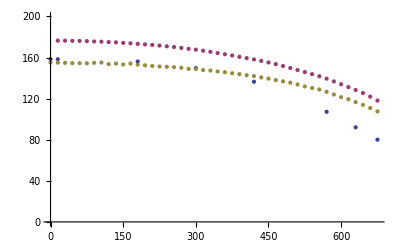

```mathematica
(*freeze-out points for the muB we computed:*)
FreezeOutCurve=Table[{FPRmuBlist[[i]],Tchemfreeze[sqrtsCF[FPRmuBlist[[i]]]]},{i,1,Length[FPRmuBlist]}]
ListPlot[{FreezeOutCurve,chiPBns0,decPBns0},PlotRange->{0,200}]
```

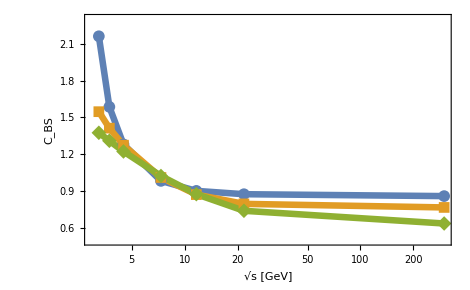

```mathematica
(*C_BS at freeze out*)
FPRTchilist={176.5,176.4458941518588,173.32950673235786,167.71292311905395,158.14475787458744,139.45938665483314,128.4726195105337,118.12858880863287};
FPRTdeclist={155.248011549924,155.0726884238329,153.0690161512399,148.87362129181713,141.9510134569225,126.66254870480044,116.61455880462226,107.59256510398743};

TFOfac=1(*(176/156)*);
CBSFOFRG=Table[{sqrtsCF[FPRmuBlist[[i]]],(CBSofTmu2s[FPRmuBlist[[i]]][[1]]+CBSofTmu2s[FPRmuBlist[[i]]][[2]])/2/.T->TFOfac Tchemfreeze[sqrtsCF[FPRmuBlist[[i]]]]},{i,2,Length[FPRmuBlist]}];
CBSFOFRGchi=Table[{sqrtsCF[FPRmuBlist[[i]]],(CBSofTmu2s[FPRmuBlist[[i]]][[1]]+CBSofTmu2s[FPRmuBlist[[i]]][[2]])/2/.T->FPRTchilist[[i]]},{i,2,Length[FPRmuBlist]}];
CBSFOFRGdec=Table[{sqrtsCF[FPRmuBlist[[i]]],(CBSofTmu2s[FPRmuBlist[[i]]][[1]]+CBSofTmu2s[FPRmuBlist[[i]]][[2]])/2/.T->FPRTdeclist[[i]]},{i,2,Length[FPRmuBlist]}];
CBSFOHRG=Table[{sqrtsCF[FPRmuBlist[[i]]],CBSHRGnS0[Tchemfreeze[sqrtsCF[FPRmuBlist[[i]]]],FPRmuBlist[[i]]]},{i,2,Length[FPRmuBlist]}];

ListLogLinearPlot[{CBSFOFRGchi,CBSFOFRG,CBSFOHRG},PlotRange->{0.5,2.3},
Joined->True,InterpolationOrder->1,
AxesOrigin->{0,1},
ImageSize->470,Frame->True,PlotRange->{{90,240},{0,2.3}},AxesOrigin->{90,0},
PlotMarkers->
{{Automatic,Offset[12]},{Automatic,Offset[11]},{Automatic,Offset[15]}},
PlotStyle->Thickness[.01],
FrameStyle->{{{Thickness[0.0025],Black},{Thickness[0.0025],Black}},{{Thickness[0.0025],Black},{Thickness[0.0025],Black}}},
FrameLabel->{Style["√s [GeV]",FontFamily->"Helvetica"],Style["C_BS",FontFamily->"Helvetica"]},
LabelStyle->{FontFamily->"Helvetica",FontSize->15,Black},
PlotRegion->{{0.02,0.98},{0.02,0.98}}]
```

### C_BS and the phase transitions

```mathematica
chiPBns0
```

{{15.,176.446},{30.,176.411},{45.,176.291},{60.,176.192},{75.,175.987},{90.,175.648},{105.,175.438},{120.,175.074},{135.,174.796},{150.,174.28},{165.,173.901},{180.,173.33},{195.,172.829},{210.,172.295},{225.,171.662},{240.,170.938},{255.,170.186},{270.,169.435},{285.,168.489},{300.,167.713},{315.,166.622},{330.,165.578},{345.,164.373},{360.,163.221},{375.,161.989},{390.,160.708},{405.,159.461},{420.,158.145},{435.,156.738},{450.,155.197},{465.,153.544},{480.,151.761},{495.,149.824},{510.,147.817},{525.,145.861},{540.,143.865},{555.,141.781},{570.,139.459},{585.,136.784},{600.,134.016},{615.,131.206},{630.,128.473},{645.,125.511},{660.,121.941},{675.,118.129}}

```mathematica
decPBns0
```

{{0.,155.248},{15.,155.073},{30.,154.814},{45.,154.537},{60.,154.463},{75.,154.388},{90.,154.84},{105.,155.155},{120.,153.608},{135.,154.189},{150.,153.266},{165.,154.179},{180.,153.069},{195.,152.452},{210.,151.806},{225.,151.286},{240.,150.947},{255.,150.676},{270.,150.073},{285.,148.961},{300.,148.874},{315.,147.824},{330.,147.343},{345.,146.487},{360.,145.737},{375.,144.738},{390.,143.844},{405.,142.81},{420.,141.951},{435.,140.661},{450.,139.459},{465.,138.011},{480.,136.85},{495.,135.582},{510.,133.785},{525.,131.861},{540.,130.338},{555.,128.847},{570.,126.663},{585.,124.028},{600.,121.418},{615.,119.448},{630.,116.615},{645.,113.956},{660.,110.883},{675.,107.593}}

```mathematica
CBSatTchiral={{176.4458941518588,(CBSofTmu2s[0][[1]]+CBSofTmu2s[0][[2]])/2/.T->176.4458941518588},
{173.32950673235786,(CBSofTmu2s[180][[1]]+CBSofTmu2s[180][[2]])/2/.T->173.32950673235786},
{167.71292311905395,(CBSofTmu2s[300][[1]]+CBSofTmu2s[300][[2]])/2/.T->167.71292311905395},
{158.14475787458744,(CBSofTmu2s[420][[1]]+CBSofTmu2s[420][[2]])/2/.T->158.14475787458744},
{139.45938665483314,(CBSofTmu2s[570][[1]]+CBSofTmu2s[570][[2]])/2/.T->139.45938665483314},
{128.4726195105337,(CBSofTmu2s[630][[1]]+CBSofTmu2s[630][[2]])/2/.T->128.4726195105337},
{118.12858880863287,(CBSofTmu2s[675][[1]]+CBSofTmu2s[675][[2]])/2/.T->118.12858880863287}};

CBSatTdeconf={{155.248011549924,(CBSofTmu2s[0][[1]]+CBSofTmu2s[0][[2]])/2/.T->155.248011549924},
{153.0690161512399,(CBSofTmu2s[180][[1]]+CBSofTmu2s[180][[2]])/2/.T->153.0690161512399},
{148.87362129181713,(CBSofTmu2s[300][[1]]+CBSofTmu2s[300][[2]])/2/.T->148.87362129181713},
{141.9510134569225,(CBSofTmu2s[420][[1]]+CBSofTmu2s[420][[2]])/2/.T->141.9510134569225},
{126.66254870480044,(CBSofTmu2s[570][[1]]+CBSofTmu2s[570][[2]])/2/.T->126.66254870480044},
{116.61455880462226,(CBSofTmu2s[630][[1]]+CBSofTmu2s[630][[2]])/2/.T->116.61455880462226},
{107.59256510398743,(CBSofTmu2s[675][[1]]+CBSofTmu2s[675][[2]])/2/.T->107.59256510398743}};
```

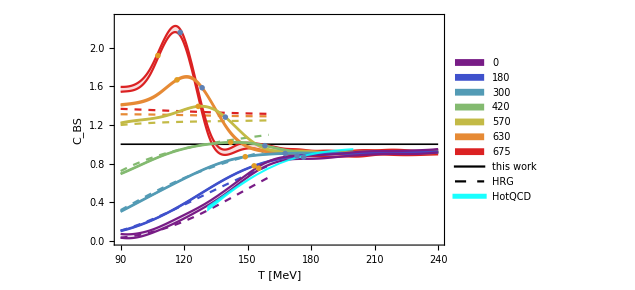

```mathematica
Show[CBSfinalPlot,ListPlot[{CBSatTchiral,CBSatTdeconf},PlotMarkers->{Black,Red}]]
```